#### Definitions

Make sure to run the code below -- but don’t worry about the details, these are just definitions of the functions our demo will use

```mathematica
SetDirectory[NotebookDirectory[]];
Import["https://qtechtheory.org/QuESTlink.m"]
CreateDownloadedQuESTEnv[];
pswap[p1_,p2_]:={{ⅇ^(-ⅈ p2),0,0,0},{0,1/2 ⅇ^(-2 ⅈ p1+ⅈ p2)+1/2 ⅇ^(2 ⅈ p1+ⅈ p2),1/2 ⅇ^(-2 ⅈ p1+ⅈ p2)-1/2 ⅇ^(2 ⅈ p1+ⅈ p2),0},{0,1/2 ⅇ^(-2 ⅈ p1+ⅈ p2)-1/2 ⅇ^(2 ⅈ p1+ⅈ p2),1/2 ⅇ^(-2 ⅈ p1+ⅈ p2)+1/2 ⅇ^(2 ⅈ p1+ⅈ p2),0},{0,0,0,ⅇ^(-ⅈ p2)}};
ccphasemat[θ_]:={{1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,ⅇ^((ⅈ θ)/2)}};

gate[c_,n1_,n2_,typ_]:=Switch[typ

,"crx",{Subscript[Ry, n1][π/2],Subscript[Rz, n2][(5 π)/2],Subscript[C, n1][Subscript[Rx, n2][π]],Subscript[Rz, n2][(7 π)/2],Subscript[C, c][Subscript[Rx, n2][(5 π)/2]],Subscript[C, c][Subscript[Rx, n1][π/2]],Subscript[C, n1][Subscript[Rx, n2][π]],Subscript[Rz, n1][(3 π)/2],Subscript[C, c][Subscript[Rx, n1][(3 π)/2]],Subscript[Ry, n1][(7 π)/2],Subscript[Rz, n2][(3 π)/2],Subscript[C, n2][Subscript[Rx, n1][π]],Subscript[Rz, c][(7 π)/4]}

,"crxUE",{Subscript[C, c][Subscript[Rx, n1][3 π]],Subscript[C, n1][Subscript[Rx, n2][ π]],Subscript[Rz, n1][(5 π)/2],Subscript[Rz, n2][(13 π)/4],Subscript[C, n2][Subscript[Rx, n1][π/2]],Subscript[C, c][Subscript[Rx, n2][3 π]],Subscript[C, c][Subscript[Rx, n1][π/2]],Subscript[Rz, c][π/4]}
,"crxOBSX",{Subscript[C, n1][Subscript[Rx, n2][π]],Subscript[Rz, n1][(5 π)/2],Subscript[Rz, n2][(15 π)/4],Subscript[C, n2][Subscript[Rx, n1][(3 π)/2]],Subscript[C, c][Subscript[Rx, n2][π]],Subscript[C, c][Subscript[Rx, n1][π/2]],Subscript[Rz, c][-π/4]}

,"xx",{Subscript[Ry, c][(7 π)/2],Subscript[Rz, n1][(7 π)/2],R[(5 π)/2,Subscript[X, n1] Subscript[X, n2]],Subscript[Rz, n1][(7 π)/4],Subscript[Rz, n2][(3 π)/4],Subscript[Ry, n1][π/2],R[(7 π)/2,Subscript[X, c] Subscript[X, n2]],Subscript[Ry, n2][(11 π)/4],R[(7 π)/2,Subscript[X, n1] Subscript[X, n2]],R[π/4,Subscript[X, c] Subscript[X, n1]],Subscript[Rz, n2][π/4],R[(5 π)/2,Subscript[X, c] Subscript[X, n2]],Subscript[Ry, c][(5 π)/2],Subscript[Rz, n1][(5 π)/2],Subscript[Ry, n2][(7 π)/4],R[(7 π)/2,Subscript[X, n1] Subscript[X, n2]],Subscript[Ry, n1][π/2],Subscript[Rz, c][(11 π)/4]}

,"xxUE",{Subscript[Ry, c][(7 π)/2],Subscript[Rz, n2][π/2],R[(7 π)/2,Subscript[X, n1] Subscript[X, n2]],R[(7 π)/2,Subscript[X, c] Subscript[X, n1]],Subscript[Ry, n1][(5 π)/4],Subscript[Ry, n2][(5 π)/2],R[(3 π)/2,Subscript[X, n1] Subscript[X, n2]],Subscript[Rz, n1][(3 π)/4],R[(11 π)/4,Subscript[X, c] Subscript[X, n2]],R[π/2,Subscript[X, c] Subscript[X, n1]],Subscript[Ry, c][π/2],Subscript[Rz, c][(5 π)/4]}
,"xxOBSX",{Subscript[Rz, n2][-π/2],R[π/2,Subscript[X, n1] Subscript[X, n2]],Subscript[Rz, n1][(3 π)/4],Subscript[Ry, n2][π/2],Subscript[Ry, c][(3 π)/2],R[(7 π)/2,Subscript[X, n1] Subscript[X, n2]],R[(5 π)/4,Subscript[X, c] Subscript[X, n2]],Subscript[Ry, n1][(3 π)/4],R[π/2,Subscript[X, c] Subscript[X, n1]],Subscript[Ry, c][π/2],Subscript[Rz, c][(5 π)/4]}

,"pswap",{Subscript[Rx, n1][π/2],Subscript[Rx, n2][(5 π)/2],Subscript[pSWAP, n1,n2][(31 π)/8,(3 π)/4],Subscript[pSWAP, n2,c][(7 π)/2,(7 π)/4],Subscript[Rz, n1][(5 π)/2],Subscript[Ry, n1][(7 π)/2],Subscript[Ry, n2][π/2],Subscript[pSWAP, n1,n2][π/8,(5 π)/2],Subscript[pSWAP, n1,c][π/4,(5 π)/2],Subscript[Rz, n2][(7 π)/2],Subscript[Ry, n2][(5 π)/2],Subscript[Ry, c][π/2],Subscript[pSWAP, n2,c][(19 π)/8,π/2],Subscript[pSWAP, n1,c][π/4,π],Subscript[Rz, n1][π/2],Subscript[Ry, n1][π/2],Subscript[Ry, n2][(7 π)/2],Subscript[Rz, c][(13 π)/4]}

,"pswapUE",{Subscript[Rz, n2][(3 π)/2],Subscript[pSWAP, n1,n2][(19 π)/8,(159 π)/200],Subscript[pSWAP, n2,c][n1,(13 π)/8],Subscript[pSWAP, n1,c][n1,(23 π)/8],Subscript[Ry, n2][(7 π)/2],Subscript[pSWAP, n1,n2][(15 π)/4,(7 π)/2],Subscript[Rz, n1][(7 π)/2],Subscript[Ry, n1][π/2],Subscript[pSWAP, n1,c][(7 π)/2,(31 π)/8],Subscript[Rz, c][(7 π)/4]}
,"pswapOBSX",{Subscript[pSWAP, 0,1][(5 π)/8,(5 π)/2],Subscript[pSWAP, 1,2][π/2,(13 π)/4],Subscript[Rz, n1][π/2],Subscript[Ry, n1][(3 π)/2],Subscript[Ry, n2][(5 π)/2],Subscript[pSWAP, 0,1][(25 π)/8,0],Subscript[pSWAP, 0,2][π,(15 π)/4],Subscript[Rz, c][(13 π)/4]}

,"cz",{Subscript[Rx, n2][(7 π)/2],Subscript[C, n1][Subscript[Rz, n2][3 π]],Subscript[Ry, n2][(3 π)/4],Subscript[Rz, n2][3 π],Subscript[C, c][Subscript[Rz, n2][π]],Subscript[Ry, n1][(5 π)/2],Subscript[Ry, n2][(7 π)/4],Subscript[C, n2][Subscript[Rz, n1][π]],Subscript[C, c][Subscript[Rz, n1][(5 π)/2]],Subscript[Rx, n1][(3 π)/2],Subscript[Rx, n2][(3 π)/4],Subscript[Rz, n1][(5 π)/2],Subscript[C, c][Subscript[Rz, n2][π]],Subscript[Rx, n1][π],Subscript[Rx, n2][π/4],Subscript[C, n2][Subscript[Rz, n1][π]],Subscript[Ry, n2][(7 π)/2],Subscript[Rx, n1][π/2],Subscript[Rx, c][n1],Subscript[Rz, n1][(7 π)/2],Subscript[Rz, n2][π/2],Subscript[Rz, c][(3 π)/4]}

,"czUE",{Subscript[Ry, n1][π/2],Subscript[C, n2][Subscript[Rz, n1][-π]],Subscript[C, c][Subscript[Rz, n1][ π]],Subscript[Rx, n1][(3 π)/4],Subscript[Rx, n2][(5 π)/2],Subscript[C, n2][Subscript[Rz, n1][- π]],Subscript[Rx, n1][(11 π)/4],Subscript[C, c][Subscript[Rz, n2][(7 π)/2]],Subscript[C, c][Subscript[Rz, n1][-π]],Subscript[Rz, c][(9 π)/4]}
,"czOBSX",{Subscript[Ry, n1][(7 π)/2],Subscript[C, n1][Subscript[Rz, n2][π]],Subscript[Ry, n2][(7 π)/2],Subscript[Rx, n1][(3 π)/2],Subscript[C, n2][Subscript[Rz, n1][(3 π)/2]],Subscript[C, c][Subscript[Rz, n2][(5 π)/2]],Subscript[Rx, n1][π/2],Subscript[C, c][Subscript[Rz, n1][π]],Subscript[Rz, c][(15 π)/4]}

,"xxx",{Subscript[Ry, c][π/2],R[(11 π)/4,Subscript[X, n1] Subscript[X, n2]],R[π/4,Subscript[X, c] Subscript[X, n1] Subscript[X, n2]],Subscript[Ry, n1][(3 π)/2],Subscript[Ry, n2][(5 π)/2],R[π/4,Subscript[X, n1] Subscript[X, n2]],R[(3 π)/4,Subscript[X, c] Subscript[X, n1] Subscript[X, n2]],Subscript[Ry, n1][π/2],Subscript[Ry, n2][(3 π)/2],Subscript[Rz, n1][(5 π)/2],Subscript[Rz, n2][(3 π)/2],R[(5 π)/4,Subscript[X, n1] Subscript[X, n2]],R[(15 π)/4,Subscript[X, c] Subscript[X, n1] Subscript[X, n2]],Subscript[Ry, c][(3 π)/2],Subscript[Rz, n1][(7 π)/2],Subscript[Rz, n2][π/2],Subscript[Rz, c][(11 π)/4]}

,"xxxUE",{Subscript[Ry, c][π/2],R[(3 π)/4,Subscript[X, c] Subscript[X, n1] Subscript[X, n2]],Subscript[Ry, n1][π/2],Subscript[Ry, n2][(7 π)/2],R[(13 π)/4,Subscript[X, c] Subscript[X, n1] Subscript[X, n2]],Subscript[Rz, n1][(5 π)/2],Subscript[Rz, n2][π/2],R[(11 π)/4,Subscript[X, c] Subscript[X, n1] Subscript[X, n2]],Subscript[Ry, c][(3 π)/2],Subscript[Rz, c][(13 π)/4]}
,"xxxOBSX",{Subscript[Ry, c][π/2],R[(5 π)/4,Subscript[X, c] Subscript[X, n1] Subscript[X, n2]],Subscript[Ry, n2][π/2],Subscript[Rz, n1][(3 π)/2],R[π/2,Subscript[X, n1] Subscript[X, n2]],Subscript[Ry, n1][(15 π)/4],Subscript[Rz, n2][(15 π)/4],R[π/2,Subscript[X, c] Subscript[X, n1] Subscript[X, n2]],Subscript[Ry, c][(3 π)/2],Subscript[Rz, c][(9 π)/4]}

,"ccphase",{Subscript[Rx, n2][(5 π)/2],Subscript[C, n2][Subscript[Rz, n1][π]],Subscript[Ry, n2][π/2],Subscript[Rx, n1][π/2],Subscript[CCPhase, c,n1,n2][2 π],Subscript[Ry, n2][(7 π)/2],Subscript[Rx, n1][(7 π)/2],Subscript[C, n2][Subscript[Rz, n1][3 π]],Subscript[Rx, n2][(3 π)/2]}
,"ccphaseUE",{Subscript[Ry, n1][(7 π)/2],Subscript[C, n2][Subscript[Rz, n1][π]],Subscript[Ry, n1][(5 π)/2],Subscript[Rx, n2][(7 π)/2],Subscript[CCPhase, c,n1,n2][2 π]}
,"ccphaseOBSX",{Subscript[Ry, n2][(5 π)/2],Subscript[C, n2][Subscript[Rz, n1][ π]],Subscript[C, c][Subscript[Rz, n2][- π]],Subscript[Ry, n1][π/2],Subscript[Rx, n2][(5 π)/2],Subscript[CCPhase, c,n1,n2][2π],Subscript[Rz, c][π/2]}
]
```

#### 1) Type A and Type B recompilations

Type A recompilation: fully equivalent recompilation of the elementary controlled-SWAP gate
Type B recompilation: the elementary controlled-SWAP gate was recompiled up to an SU(4) freedom on the two swapped qubits

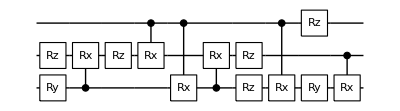
Gate Type: crx
#2-qubit gates:  6
#1-qubit gates:  7(-1) by removing the Z gate at the end
-Graphics-
{Ry_n1[π/2],Rz_n2[(5 π)/2],C_n1[Rx_n2[π]],Rz_n2[(7 π)/2],C_c[Rx_n2[(5 π)/2]],C_c[Rx_n1[π/2]],C_n1[Rx_n2[π]],Rz_n1[(3 π)/2],C_c[Rx_n1[(3 π)/2]],Ry_n1[(7 π)/2],Rz_n2[(3 π)/2],C_n2[Rx_n1[π]],Rz_c[(7 π)/4]}
is the circuit correct:   True

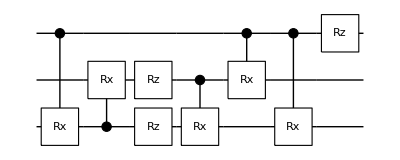
Gate Type: crxUE
#2-qubit gates:  5
#1-qubit gates:  3(-1) by removing the Z gate at the end
-Graphics-
{C_c[Rx_n1[3 π]],C_n1[Rx_n2[π]],Rz_n1[(5 π)/2],Rz_n2[(13 π)/4],C_n2[Rx_n1[π/2]],C_c[Rx_n2[3 π]],C_c[Rx_n1[π/2]],Rz_c[π/4]}
is the circuit correct:   True

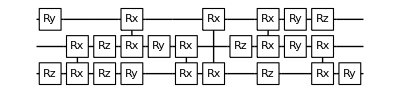
Gate Type: xx
#2-qubit gates:  6
#1-qubit gates:  12(-1) by removing the Z gate at the end
-Graphics-
{Ry_c[(7 π)/2],Rz_n1[(7 π)/2],R[(5 π)/2,X_n1 X_n2],Rz_n1[(7 π)/4],Rz_n2[(3 π)/4],Ry_n1[π/2],R[(7 π)/2,X_c X_n2],Ry_n2[(11 π)/4],R[(7 π)/2,X_n1 X_n2],R[π/4,X_c X_n1],Rz_n2[π/4],R[(5 π)/2,X_c X_n2],Ry_c[(5 π)/2],Rz_n1[(5 π)/2],Ry_n2[(7 π)/4],R[(7 π)/2,X_n1 X_n2],Ry_n1[π/2],Rz_c[(11 π)/4]}
is the circuit correct:   True

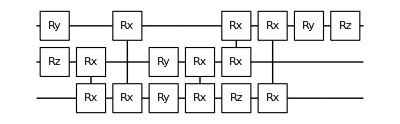
Gate Type: xxUE
#2-qubit gates:  5
#1-qubit gates:  7(-1) by removing the Z gate at the end
-Graphics-
{Ry_c[(7 π)/2],Rz_n2[π/2],R[(7 π)/2,X_n1 X_n2],R[(7 π)/2,X_c X_n1],Ry_n1[(5 π)/4],Ry_n2[(5 π)/2],R[(3 π)/2,X_n1 X_n2],Rz_n1[(3 π)/4],R[(11 π)/4,X_c X_n2],R[π/2,X_c X_n1],Ry_c[π/2],Rz_c[(5 π)/4]}
is the circuit correct:   True

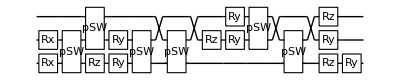
Gate Type: pswap
#2-qubit gates:  6
#1-qubit gates:  12(-1) by removing the Z gate at the end
-Graphics-
{Rx_n1[π/2],Rx_n2[(5 π)/2],pSWAP_(n1,n2)[(31 π)/8,(3 π)/4],pSWAP_(n2,c)[(7 π)/2,(7 π)/4],Rz_n1[(5 π)/2],Ry_n1[(7 π)/2],Ry_n2[π/2],pSWAP_(n1,n2)[π/8,(5 π)/2],pSWAP_(n1,c)[π/4,(5 π)/2],Rz_n2[(7 π)/2],Ry_n2[(5 π)/2],Ry_c[π/2],pSWAP_(n2,c)[(19 π)/8,π/2],pSWAP_(n1,c)[π/4,π],Rz_n1[π/2],Ry_n1[π/2],Ry_n2[(7 π)/2],Rz_c[(13 π)/4]}
is the circuit correct:   True

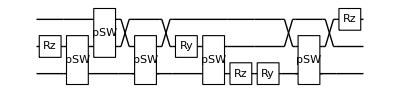
Gate Type: pswapUE
#2-qubit gates:  5
#1-qubit gates:  5(-1) by removing the Z gate at the end
-Graphics-
{Rz_n2[(3 π)/2],pSWAP_(n1,n2)[(19 π)/8,(159 π)/200],pSWAP_(n2,c)[n1,(13 π)/8],pSWAP_(n1,c)[n1,(23 π)/8],Ry_n2[(7 π)/2],pSWAP_(n1,n2)[(15 π)/4,(7 π)/2],Rz_n1[(7 π)/2],Ry_n1[π/2],pSWAP_(n1,c)[(7 π)/2,(31 π)/8],Rz_c[(7 π)/4]}
is the circuit correct:   True

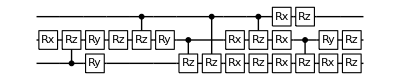
Gate Type: cz
#2-qubit gates:  6
#1-qubit gates:  16(-1) by removing the Z gate at the end
-Graphics-
{Rx_n2[(7 π)/2],C_n1[Rz_n2[3 π]],Ry_n2[(3 π)/4],Rz_n2[3 π],C_c[Rz_n2[π]],Ry_n1[(5 π)/2],Ry_n2[(7 π)/4],C_n2[Rz_n1[π]],C_c[Rz_n1[(5 π)/2]],Rx_n1[(3 π)/2],Rx_n2[(3 π)/4],Rz_n1[(5 π)/2],C_c[Rz_n2[π]],Rx_n1[π],Rx_n2[π/4],C_n2[Rz_n1[π]],Ry_n2[(7 π)/2],Rx_n1[π/2],Rx_c[n1],Rz_n1[(7 π)/2],Rz_n2[π/2],Rz_c[(3 π)/4]}
is the circuit correct:   True

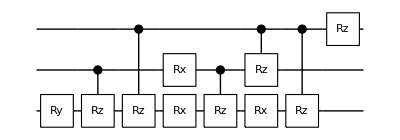
Gate Type: czUE
#2-qubit gates:  5
#1-qubit gates:  5(-1) by removing the Z gate at the end
-Graphics-
{Ry_n1[π/2],C_n2[Rz_n1[-π]],C_c[Rz_n1[π]],Rx_n1[(3 π)/4],Rx_n2[(5 π)/2],C_n2[Rz_n1[-π]],Rx_n1[(11 π)/4],C_c[Rz_n2[(7 π)/2]],C_c[Rz_n1[-π]],Rz_c[(9 π)/4]}
is the circuit correct:   True

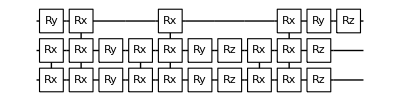
Gate Type: xxx
#2-qubit gates:  6
#1-qubit gates:  11(-1) by removing the Z gate at the end
-Graphics-
{Ry_c[π/2],R[(11 π)/4,X_n1 X_n2],R[π/4,X_c X_n1 X_n2],Ry_n1[(3 π)/2],Ry_n2[(5 π)/2],R[π/4,X_n1 X_n2],R[(3 π)/4,X_c X_n1 X_n2],Ry_n1[π/2],Ry_n2[(3 π)/2],Rz_n1[(5 π)/2],Rz_n2[(3 π)/2],R[(5 π)/4,X_n1 X_n2],R[(15 π)/4,X_c X_n1 X_n2],Ry_c[(3 π)/2],Rz_n1[(7 π)/2],Rz_n2[π/2],Rz_c[(11 π)/4]}
is the circuit correct:   True

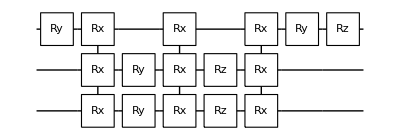
Gate Type: xxxUE
#2-qubit gates:  3
#1-qubit gates:  7(-1) by removing the Z gate at the end
-Graphics-
{Ry_c[π/2],R[(3 π)/4,X_c X_n1 X_n2],Ry_n1[π/2],Ry_n2[(7 π)/2],R[(13 π)/4,X_c X_n1 X_n2],Rz_n1[(5 π)/2],Rz_n2[π/2],R[(11 π)/4,X_c X_n1 X_n2],Ry_c[(3 π)/2],Rz_c[(13 π)/4]}
is the circuit correct:   True

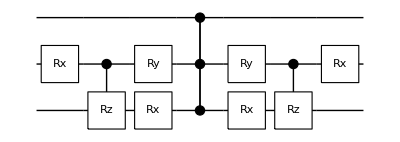
Gate Type: ccphase
#2-qubit gates:  3
#1-qubit gates:  6(-1) by removing the Z gate at the end
-Graphics-
{Rx_n2[(5 π)/2],C_n2[Rz_n1[π]],Ry_n2[π/2],Rx_n1[π/2],CCPhase_(c,n1,n2)[2 π],Ry_n2[(7 π)/2],Rx_n1[(7 π)/2],C_n2[Rz_n1[3 π]],Rx_n2[(3 π)/2]}
is the circuit correct:   True

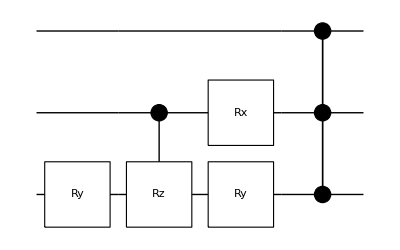
Gate Type: ccphaseUE
#2-qubit gates:  2
#1-qubit gates:  3(-1) by removing the Z gate at the end
-Graphics-
{Ry_n1[(7 π)/2],C_n2[Rz_n1[π]],Ry_n1[(5 π)/2],Rx_n2[(7 π)/2],CCPhase_(c,n1,n2)[2 π]}
is the circuit correct:   True

```mathematica
ρ=CreateDensityQureg[3];
gateCanDo={"crx","crxUE","xx","xxUE","pswap","pswapUE","cz","czUE","xxx","xxxUE","ccphase","ccphaseUE"};
dat={};
Do[
gateTyp=gateCanDo[[k]];
cSWAPCirc=gate[2,0,1,gateTyp];
circ=Flatten@{Subscript[H, 2],cSWAPCirc,Subscript[H, 2]}/.{Subscript[pSWAP, n1_,n2_][p1_,p2_]:>Subscript[U, n1,n2][pswap[p1,p2]],Subscript[CCPhase, c_,n1_,n2_][p1_]:>Subscript[U, c,n1,n2][ccphasemat[p1]]};
twoQubitGateCount=Count[cSWAPCirc,R[__]|Subscript[U, __][__]|Subscript[C, __][__]|Subscript[CCPhase, __][__]|Subscript[pSWAP, __][__]];
rand=With[{r=RandomComplex[{-1-ⅈ,1+ⅈ},{2,2}]},
	r . r† / Tr[r . r†]];
SetQuregMatrix[ρ,KroneckerProduct[{{1,0},{0,0}},KroneckerProduct[rand,rand]]];
ApplyCircuit[circ,ρ];
circPic=DrawCircuit[cSWAPCirc/.{Subscript[CCPhase, c_,n1_,n2_][__]:>Subscript[C, c,n1][Subscript[Z, n2]],Subscript[pSWAP, n1_,n2_][__]:>Subscript[pSW, n1,n2]},ImageSize->{Automatic,60},FontFamily->"Times New Roman"];
AppendTo[dat,{circPic,twoQubitGateCount,Length@cSWAPCirc-twoQubitGateCount}];
Print["Gate Type: ",gateTyp,"\n#2-qubit gates:  " ,twoQubitGateCount,"\n#1-qubit gates:  ",Length@cSWAPCirc-twoQubitGateCount,"(-1) by removing the Z gate at the end\n",
circPic
,"\n",gate[c,n1,n2,gateTyp],
 "\nis the circuit correct:   "
,Chop[2CalcProbOfOutcome[ρ,2,0]-1-Tr[rand.rand]]==0,"\n\n"
];
,{k,1,Length@gateCanDo}]

DestroyAllQuregs[];
```

#### 1) Type C recompilations

Type C recompilation: the product of the elementary controlled-SWAP gate and the controlled X observable was recompiled up to an SU(4) freedom on the two swapped qubits

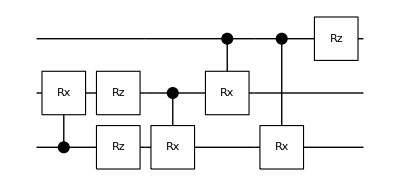
Gate Type: crxOBSX
#2-qubit gates:  4
#1-qubit gates:  3(-1) by removing the Z gate at the end
-Graphics-
{C_n1[Rx_n2[π]],Rz_n1[(5 π)/2],Rz_n2[(15 π)/4],C_n2[Rx_n1[(3 π)/2]],C_c[Rx_n2[π]],C_c[Rx_n1[π/2]],Rz_c[-π/4]}
is the circuit correct:   True

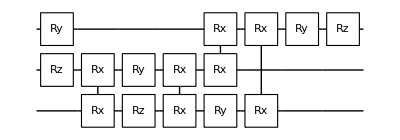
Gate Type: xxOBSX
#2-qubit gates:  4
#1-qubit gates:  7(-1) by removing the Z gate at the end
-Graphics-
{Rz_n2[-π/2],R[π/2,X_n1 X_n2],Rz_n1[(3 π)/4],Ry_n2[π/2],Ry_c[(3 π)/2],R[(7 π)/2,X_n1 X_n2],R[(5 π)/4,X_c X_n2],Ry_n1[(3 π)/4],R[π/2,X_c X_n1],Ry_c[π/2],Rz_c[(5 π)/4]}
is the circuit correct:   True

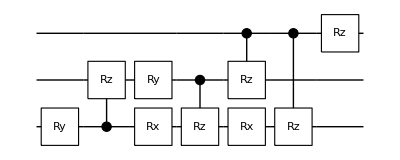
Gate Type: czOBSX
#2-qubit gates:  4
#1-qubit gates:  5(-1) by removing the Z gate at the end
-Graphics-
{Ry_n1[(7 π)/2],C_n1[Rz_n2[π]],Ry_n2[(7 π)/2],Rx_n1[(3 π)/2],C_n2[Rz_n1[(3 π)/2]],C_c[Rz_n2[(5 π)/2]],Rx_n1[π/2],C_c[Rz_n1[π]],Rz_c[(15 π)/4]}
is the circuit correct:   True

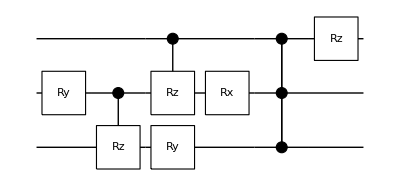
Gate Type: ccphaseOBSX
#2-qubit gates:  3
#1-qubit gates:  4(-1) by removing the Z gate at the end
-Graphics-
{Ry_n2[(5 π)/2],C_n2[Rz_n1[π]],C_c[Rz_n2[-π]],Ry_n1[π/2],Rx_n2[(5 π)/2],CCPhase_(c,n1,n2)[2 π],Rz_c[π/2]}
is the circuit correct:   True

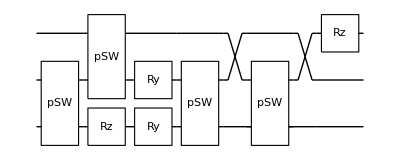
Gate Type: pswapOBSX
#2-qubit gates:  4
#1-qubit gates:  4(-1) by removing the Z gate at the end
-Graphics-
{pSWAP_(0,1)[(5 π)/8,(5 π)/2],pSWAP_(1,2)[π/2,(13 π)/4],Rz_n1[π/2],Ry_n1[(3 π)/2],Ry_n2[(5 π)/2],pSWAP_(0,1)[(25 π)/8,0],pSWAP_(0,2)[π,(15 π)/4],Rz_c[(13 π)/4]}
is the circuit correct:   True

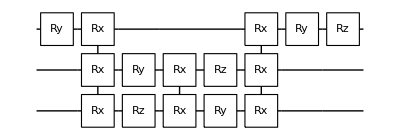
Gate Type: xxxOBSX
#2-qubit gates:  3
#1-qubit gates:  7(-1) by removing the Z gate at the end
-Graphics-
{Ry_c[π/2],R[(5 π)/4,X_c X_n1 X_n2],Ry_n2[π/2],Rz_n1[(3 π)/2],R[π/2,X_n1 X_n2],Ry_n1[(15 π)/4],Rz_n2[(15 π)/4],R[π/2,X_c X_n1 X_n2],Ry_c[(3 π)/2],Rz_c[(9 π)/4]}
is the circuit correct:   True

```mathematica
ρ=CreateDensityQureg[3];
gateCanDo={"crxOBSX","xxOBSX","czOBSX","ccphaseOBSX","pswapOBSX","xxxOBSX"};
dat={};
Do[
gateTyp=gateCanDo[[k]];
cSWAPCirc=gate[2,0,1,gateTyp];
circ=Flatten@{Subscript[H, 2],cSWAPCirc,Subscript[H, 2]}/.{Subscript[pSWAP, n1_,n2_][p1_,p2_]:>Subscript[U, n1,n2][pswap[p1,p2]],Subscript[CCPhase, c_,n1_,n2_][p1_]:>Subscript[U, c,n1,n2][ccphasemat[p1]]};
twoQubitGateCount=Count[cSWAPCirc,R[__]|Subscript[U, __][__]|Subscript[C, __][__]|Subscript[CCPhase, __][__]|Subscript[pSWAP, __][__]];
rand=With[{r=RandomComplex[{-1-ⅈ,1+ⅈ},{2,2}]},
	r . r† / Tr[r . r†]];
SetQuregMatrix[ρ,KroneckerProduct[{{1,0},{0,0}},KroneckerProduct[rand,rand]]];
ApplyCircuit[circ,ρ];
circPic=DrawCircuit[cSWAPCirc/.{Subscript[CCPhase, c_,n1_,n2_][__]:>Subscript[C, c,n1][Subscript[Z, n2]],Subscript[pSWAP, n1_,n2_][__]:>Subscript[pSW, n1,n2]},ImageSize->{Automatic,60},FontFamily->"Times New Roman"];
AppendTo[dat,{circPic,twoQubitGateCount,Length@cSWAPCirc-twoQubitGateCount}];
Print["Gate Type: ",gateTyp,"\n#2-qubit gates:  " ,twoQubitGateCount,"\n#1-qubit gates:  ",Length@cSWAPCirc-twoQubitGateCount,"(-1) by removing the Z gate at the end\n",
circPic
,"\n",gate[c,n1,n2,gateTyp],
 "\nis the circuit correct:   "
,Chop[2CalcProbOfOutcome[ρ,2,0]-1-Tr[rand.rand.PauliMatrix[1]]]==0,"\n\n"
];
,{k,1,Length@gateCanDo}]

DestroyAllQuregs[];
```